## c)

## Defining constants

```mathematica
pc=3.086 10^16 (*Parsecs to meters*);
n=nxy=128(*Number of zones along x and y*);
nz=n; (*Number of zones along z*);
G=6.674 10^-11 (*Gravitational constant*);
Lxy=30 10^3 pc (*Length of the box along x and y directions*);
Lz=1 10^3 pc (*Length of the box along z direction*);
```

```mathematica
p0=8 10^10 1.99 10^30 /(10^3 pc)^3;
r0=10^3 pc;
h=.1 10^3 pc;
```

## Green’s function

```mathematica
fkG=If[#1==#2==#3==1,0,-G Lxy/n Lxy/n Lz/nz /( (Lxy^2/n^2 Min[#1,2n+1-#1]^2+Lxy^2/n^2 Min[#2,2n+1-#2]^2+Lz^2/nz^2Min[#3,2nz+1-#3]^2)^.5)]&;
mkG=Array[fkG,{2n,2n,2nz}];
```

The array mkG stores the values of the the Green’s function in real space.

## Fourier transform of the Green’s function

```mathematica
FmkG=Fourier[mkG];
```

The array FmkG stores the values of the the Green’s function in fourier space.

## Density function

```mathematica
Pk=p0(1+((#1-Lxy/2)^2+(#2-Lxy/2)^2)/r0^2)^(-3/2) Exp[-Abs[#3-Lz/2]/h]&;
mkn=ConstantArray[0,{2n,2n,2nz}];
mkn[[1;;n,1;;n,1;;nz]]=Table[Pk[i Lxy/n,j Lxy/n,k Lz/nz],{i,1,n},{j,1,n},{k,1,nz}];
```

The array mkn stores the values of the density in real space.

## Fourier transform of density function

```mathematica
Fmkn=Fourier[mkn];
```

Fmkn is the fourier transform of the density array.

## Inverse fourier transform of the product

```mathematica
mkSol=Re[InverseFourier[Fmkn *FmkG]][[1;;n,1;;n,1;;nz]];
```

The array mkSol now contains the values of gravitational potential.

## Plot of potential along x-axis passing through the center of the disk

```mathematica
S=mkSol[[n/2,1;;n,nz/2]];X=Range[n]Lxy/n;
```

```mathematica
ListPlot[Transpose[{X,-S}],AxesLabel->{HoldForm["x"],HoldForm["ϕ"]},PlotLabel->HoldForm["|Potential| vs x coordinate"]]
```

-Graphics-

## Finding average radial potential on the disk

```mathematica
gridk=Flatten[Table[{Floor[Sqrt[1.0(i-n/2+.5)^2+(j-n/2+.5)^2]],mkSol[[i,j,nz/2]]},{i,1,n},{j,1,n}],1];
```

Calculating average potential of all zones within a shell

```mathematica
Vkr=Table[Mean[Select[gridk,#[[1]]==j&][[All,2]]],{j,1,n/2}];
```

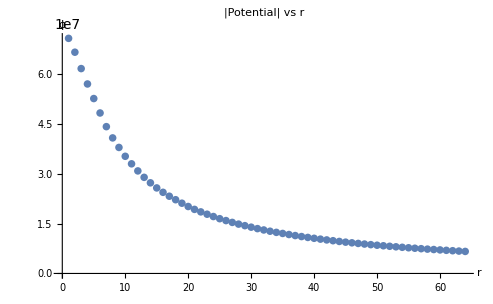

```mathematica
ListPlot[-Vkr,AxesLabel->{HoldForm["r"],HoldForm["ϕ"]},PlotLabel->HoldForm["|Potential| vs r"]]
```

Finding an interpolating function passing through these points

## Interpolation to find derivatives

```mathematica
fR=Interpolation[Transpose[{(Range[n/2,n]-n/2)Lxy/n,-mkSol[[Floor[n/2];;n,n/2,nz/2]]}]]
```

20
InterpolatingFunction[{{0., 4.629 10  }}, <>]

```mathematica
Plot[fR[x],{x,0.,4.629*^20},Frame->True,AxesLabel->{HoldForm["r"],HoldForm["ϕ"]},PlotLabel->HoldForm["|Potential| vs r"]]
```

-Graphics-

## Circular orbit frequency

```mathematica
wc[R_]=Sqrt[R  D[-fR[R],R]]
```

√(-R                                     20
InterpolatingFunction[{{0., 4.629 10  }}, <>][R])

```mathematica
Plot[wc[x],{x,0.,4.629*^20},Frame->True,AxesLabel->{HoldForm["r"],HoldForm["ϕ"]},PlotLabel->HoldForm["Circular orbit frequency vs r"]]
```

-Graphics-

## Epicyclic frequency

The epicyclic frequency k(R) is given by:

```mathematica
k[R_]=Sqrt[  D[-fR[R],{R,2}]]
```

√(-                                    20
InterpolatingFunction[{{0., 4.629 10  }}, <>][R])

```mathematica
Plot[{k[x]},{x,0.,4.629*^20},Frame->True,AxesLabel->{HoldForm["r"],HoldForm["ϕ"]},PlotLabel->HoldForm["Epicyclic frequency vs r"],PlotRange->All]
```

-Graphics-

## Corotation radius

Ω_b=wb

```mathematica
wb=10^-7/(365  24 60 60.0)
```

3.17098×10^-15

The corotation radius (Rc) is that value of R at which k(R)=wb

Inner Lindbald resonance occurs when k(R)>wb => R<Rc

Outer Lindbald resonance occurs when k(R)<wb => R>Rc